```mathematica
k0 = 2 Pi / 5;
EnergFunc[k_]:=3/2  DiracDelta[k-k0];
```

```mathematica
RhsFunc[r_]=Integrate[EnergFunc[k] Sin[k*r]/(k r),{k, 0, Infinity}];
```

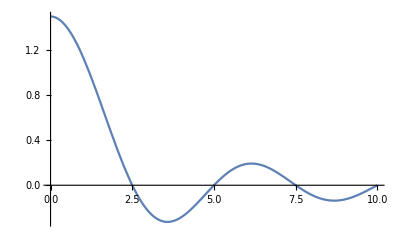

```mathematica
Plot[RhsFunc[r],{r,0,10}]
```